```mathematica
DateString[]
$Version
```

Thu 9 Mar 2023 09:15:52

13.2.0 for Microsoft Windows (64-bit) (November 18, 2022)

## Lecture 03 by Chi-Ok Hwang

[1] S. Wolfram, An Elementary Introduction to the Wolfram Language, 2nd ed. Wolfram Media, Inc., 2017.

-Graphics-

As I told you, we will choose chapters selectively.

## 9 Interactive Manipulation

9 Interactive Manipulation

```mathematica
Manipulate[Table[Orange,n],{n,0,6,2}]
```

Picky exercises: 7, 8, 15

## 10 Images

10 Images

```mathematica
ColorNegate[-Graphics-]
```

-Graphics-

```mathematica
Blur[-Graphics-,5]
```

-Graphics-

```mathematica
EdgeDetect[-Graphics-]
```

-Graphics-

CurrentImage

ColorNegate

Blur

ImageCollage

DominantColors

Binarize

EdgeDetect

ImageAdd

Picky exercises: 1, 2, 3, 4, 5, 6, 12, 13, 14, +1, +3

## 11 Strings and Text

11 Strings and Text

```mathematica
StringLength["Today is a good day!"]
```

20

```mathematica
StringReverse["DOG"]
```

GOD

Entering a text

StringLength

StringReverse

ToUpperCase

StringTake

StringJoin

Characters

Sort

TextWords

TextSentences

WordCloud

RomanNumeral

Alphabet

LetterNumber

FromLetterNumber

Transliterate

Rasterize

Picky exercises: 6, 7, 14, 16, 24, 26, 27, 29, +1, +2, +13

## 12 Sound

12 Sound

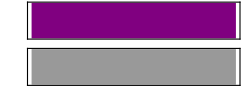

```mathematica
Sound[SoundNote["C"]]
```

Picky exercises: 7, +1, +2, +3, +4

## 13 Arrays, or Lists of Lists

13 Arrays, or Lists of Lists

```mathematica
Grid[Table[x,4,5]]
```

x | x | x | x | x
x | x | x | x | x
x | x | x | x | x
x | x | x | x | x

Picky exercises: 7

## 14 Coordinates and Graphics

14 Coordinates and Graphics

```mathematica
Manipulate[Graphics3D[{Sphere[{0,0,0}],Style[Sphere[{x,0,0}],Opacity[o]]}],{x,1,3},{o,0.5,1}]
```

ListPlot

ListLinePlot

Graphics

Picky exercises: 2, 6, 7, 10

## 15 Scope of the Wolfram Language *

15 Scope of the Wolfram Language

more than 5000 functions  --> Documentation center -> Example) Plane Geometry; Parallelgram

## 16 Real-World Data

16 Real-World Data

```mathematica
LinguisticAssistant
```

United States



```mathematica
Entity["Country","UnitedStates"]["Flag"]
```


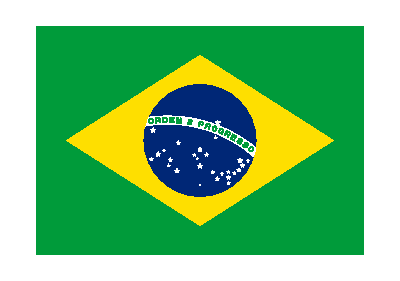


```mathematica
EntityValue[{Entity["Country","Japan"],Entity["Country","Brazil"],Entity["Country","China"]},"Flag"]
```

EntityList

Picky exercises: 11, 12, +1

What Do Data Scientists Do?

Identifying the data-analytics problems that offer the greatest opportunities to the organization

Determining the correct data sets and variables

Collecting large sets of structured and unstructured data from disparate sources

Cleaning and validating the data to ensure accuracy, completeness, and uniformity

Devising and applying models and algorithms to mine the stores of big data

Analyzing the data to identify patterns and trends

Interpreting the data to discover solutions and opportunities

Communicating findings to stakeholders using visualization and other means

## 17 Units

17 Units

```mathematica
LinguisticAssistant
```

1.2 h

```mathematica
Quantity[1.2,"Hours"]
```

1.2 h

```mathematica
CurrencyConvert[Quantity[1000.,"Won"],Quantity[1,"USDollars"]]
```

0.76 $

UnitConvert

CurrencyConvert

As a variable in Rotate function

Picky exercises: 4, 7, 8, 12, 13, +5

The Planets Today.com